```mathematica
ClearAll[θ1,θ2]
q=(T^3/(ΘA ΘB ΘC))^(1/2)(1+θ1/T+θ2/T^2)(1+ρT)
```

(1+θ1/T+θ2/T^2) √(T^3/(ΘA ΘB ΘC)) (1+ρT)

```mathematica
FullSimplify[ D[Log[q],T]]
```

-1/(2 T)+(2 T+θ1)/(T (T+θ1)+θ2)

```mathematica
FullSimplify[D[(-1/(2 T)+(2 T+θ1)/(T (T+θ1)+θ2))T^2,T]]
```

(T^2 (3 T^2+6 T θ1+θ1^2)+2 T (5 T+θ1) θ2-θ2^2)/(2 (T (T+θ1)+θ2)^2)

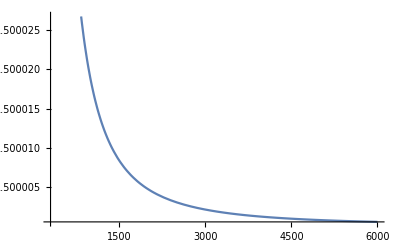

```mathematica
θ1=4.448;
θ2=19.39;
Plot[(T^2 (3 T^2+6 T θ1+θ1^2)+2 T (5 T+θ1) θ2-θ2^2)/(2 (T (T+θ1)+θ2)^2),{T,300,6000}]
```